```mathematica
Simple
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{{s→InterpolatingFunction[{{0., 500.}}, <>],i→InterpolatingFunction[{{0., 500.}}, <>],r→InterpolatingFunction[{{0., 500.}}, <>],p→InterpolatingFunction[{{0., 500.}}, <>]}}

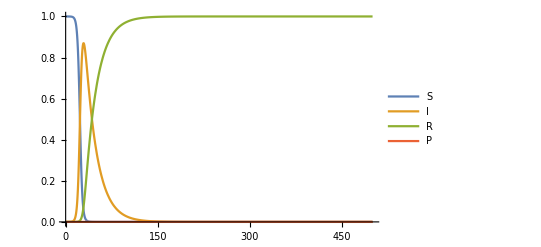

```mathematica
bt=0.5;b=1; c=0; m=.04;a=1-b-c; T=5;
system={
s'[t]==-bt s[t] i[t]+m(1-b-c)i[t-T],
i'[t]==bt s[t] i[t]-m(a+b+c) i[t-T], 
r'[t]==m b i[t-T],
p'[t]==m c i[t-T],
s[0]==1-.00001,i[0]==.00001, r[0]==0, p[0]==0};
sol=NDSolve[system,{s,i,r,p},{t,0,500}]
Plot[Evaluate[{s[t],i[t],r[t],p[t]}/.sol],{t,0,500},PlotRange->Full,PlotLegends->{"S","I","R","P"}]
```

```mathematica
w/o Immunity
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{{s→InterpolatingFunction[{{0., 500.}}, <>],i→InterpolatingFunction[{{0., 500.}}, <>],r→InterpolatingFunction[{{0., 500.}}, <>],p→InterpolatingFunction[{{0., 500.}}, <>]}}

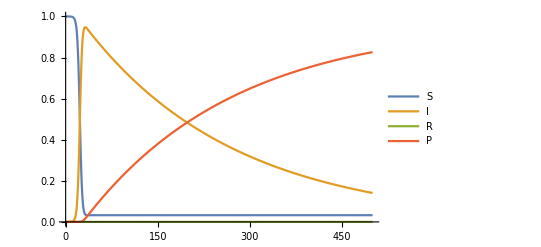

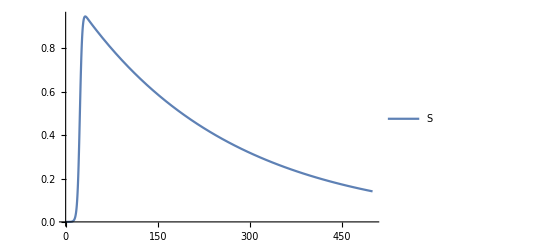

```mathematica
bt=0.5;b=0; c=.2; m=.02;a=1-b-c; T=5;
system={
s'[t]==-bt s[t] i[t]+m(1-b-c)i[t-T],
i'[t]==bt s[t] i[t]-m(a+b+c) i[t-T], 
r'[t]==m b i[t-T],
p'[t]==m c i[t-T],
s[0]==1-.00001,i[0]==.00001, r[0]==0, p[0]==0};
sol=NDSolve[system,{s,i,r,p},{t,0,500}]
Plot[Evaluate[{s[t],i[t],r[t],p[t]}/.sol],{t,0,500},PlotRange->Full,PlotLegends->{"S","I","R","P"}]
bplot=Plot[Evaluate[{i[t]}/.sol],{t,0,500},PlotRange->Full,PlotLegends->{"S","I","R","P"}]
```

```mathematica
set N = s+i+r+p, N-i=s+r+p
```

```mathematica
With Immunity
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{{s→InterpolatingFunction[{{0., 500.}}, <>],i→InterpolatingFunction[{{0., 500.}}, <>],r→InterpolatingFunction[{{0., 500.}}, <>],p→InterpolatingFunction[{{0., 500.}}, <>]}}

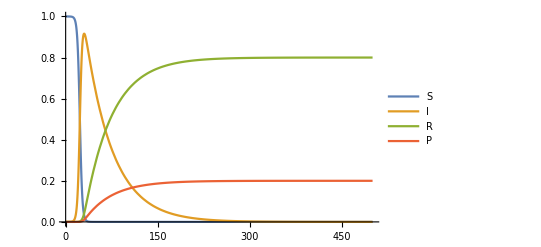

```mathematica
bt=0.5;b=1-c; c=.2; m=.02;a=1-b-c; T=5;
system={
s'[t]==-bt s[t] i[t]+m(1-b-c)i[t-T],
i'[t]==bt s[t] i[t]-m(a+b+c) i[t-T], 
r'[t]==m b i[t-T],
p'[t]==m c i[t-T],
s[0]==1-.00001,i[0]==.00001, r[0]==0, p[0]==0};
sol=NDSolve[system,{s,i,r,p},{t,0,500}]
aplot=Plot[Evaluate[{s[t],i[t],r[t],p[t]}/.sol],{t,0,500},PlotRange->Full,PlotLegends->{"S","I","R","P"}]
```

```mathematica
Fitting w/o Immunity
```

```mathematica
data=Import["C:\\Users\\cfay\\Desktop\\d100k-1_2-01-05-45.txt", {"Data",  {All}, {1, 3}}]
```

{{0,0.01416},{1,0.02243},{2,0.0317},{3,0.04098},{4,0.05073},{5,0.06073},{6,0.07131},{7,0.08205},{8,0.09318},{9,0.10498},{10,0.11745},{11,0.12238},{12,0.12733},{13,0.13067},{14,0.1338},{15,0.13611},{16,0.138},{17,0.13989},{18,0.14103},{19,0.1424},{20,0.14308},{21,0.14328},{22,0.14221},{23,0.14181},{24,0.14061},{25,0.13941},{26,0.13809},{27,0.13717},{28,0.1364},{29,0.13521},{30,0.13403},{31,0.1319},{32,0.12965},{33,0.12821},{34,0.12641},{35,0.12484},{36,0.1235},{37,0.12251},{38,0.12073},{39,0.1194},{40,0.1174},{41,0.11585},{42,0.11399},{43,0.11218},{44,0.11056},{45,0.10819},{46,0.10643},{47,0.10531},{48,0.1042},{49,0.10253},{50,0.10106},{51,0.09905},{52,0.0978},{53,0.09655},{54,0.09548},{55,0.09497},{56,0.09442},{57,0.09361},{58,0.09259},{59,0.09125},{60,0.08931},{61,0.0889},{62,0.08788},{63,0.0872},{64,0.08582},{65,0.08419},{66,0.08329},{67,0.08188},{68,0.08061},{69,0.07979},{70,0.07888},{71,0.07812},{72,0.07752},{73,0.07618},{74,0.07535},{75,0.0743},{76,0.0738},{77,0.07318},{78,0.07176},{79,0.07093},{80,0.07034},{81,0.06953},{82,0.06937},{83,0.0682},{84,0.06721},{85,0.06638},{86,0.06594},{87,0.06581},{88,0.06586},{89,0.06513},{90,0.06462},{91,0.06398},{92,0.06306},{93,0.06196},{94,0.06135},{95,0.06074},{96,0.06041},{97,0.05996},{98,0.05896},{99,0.05814},{100,0.05688},{101,0.05625},{102,0.05577},{103,0.05505},{104,0.05472},{105,0.05445},{106,0.05361},{107,0.05322},{108,0.0526},{109,0.05191},{110,0.05127},{111,0.05105},{112,0.05064},{113,0.05019},{114,0.04952},{115,0.04945},{116,0.04904},{117,0.04868},{118,0.04846},{119,0.04756},{120,0.0472},{121,0.04674},{122,0.04656},{123,0.04608},{124,0.0456},{125,0.045},{126,0.04498},{127,0.04483},{128,0.0444},{129,0.04398},{130,0.04308},{131,0.04308},{132,0.04274},{133,0.0427},{134,0.04236},{135,0.04158},{136,0.04093},{137,0.0408},{138,0.04057},{139,0.04039},{140,0.04011},{141,0.0399},{142,0.0401},{143,0.03992},{144,0.03974},{145,0.03922},{146,0.0389},{147,0.03876},{148,0.03926},{149,0.03903},{150,0.03858},{151,0.03798},{152,0.03782},{153,0.03727},{154,0.03685},{155,0.03675},{156,0.03666},{157,0.03646},{158,0.03627},{159,0.03588},{160,0.03544},{161,0.0355},{162,0.03531},{163,0.03486},{164,0.03431},{165,0.0341},{166,0.03381},{167,0.03331},{168,0.0329},{169,0.03273},{170,0.03242},{171,0.03241},{172,0.03164},{173,0.03094},{174,0.03069},{175,0.03073},{176,0.03056},{177,0.03042},{178,0.03028},{179,0.02991},{180,0.02905},{181,0.02893},{182,0.02853},{183,0.02862},{184,0.02847},{185,0.02848},{186,0.02843},{187,0.02797},{188,0.028},{189,0.0281},{190,0.02774},{191,0.02807},{192,0.02848},{193,0.02815},{194,0.02828},{195,0.02777},{196,0.02774},{197,0.02769},{198,0.02742},{199,0.02746},{200,0.02738},{201,0.02689},{202,0.02676},{203,0.02618},{204,0.02552},{205,0.02507},{206,0.02505},{207,0.02477},{208,0.02475},{209,0.02442},{210,0.02437},{211,0.02413},{212,0.02383},{213,0.02352},{214,0.02345},{215,0.02354},{216,0.02345},{217,0.0236},{218,0.02319},{219,0.02326},{220,0.02311},{221,0.02318},{222,0.02324},{223,0.02309},{224,0.02298},{225,0.02301},{226,0.02263},{227,0.02246},{228,0.02259},{229,0.02256},{230,0.02239},{231,0.02236},{232,0.02212},{233,0.02197},{234,0.0215},{235,0.02139},{236,0.02118},{237,0.02099},{238,0.02135},{239,0.021},{240,0.02115},{241,0.02091},{242,0.02051},{243,0.02011},{244,0.02025},{245,0.02004},{246,0.02019},{247,0.02012},{248,0.02003},{249,0.02017},{250,0.01996},{251,0.01979},{252,0.01945},{253,0.01941},{254,0.01983},{255,0.01995},{256,0.01976},{257,0.01975},{258,0.01943},{259,0.01937},{260,0.01934},{261,0.01902},{262,0.01869},{263,0.01882},{264,0.01894},{265,0.01882},{266,0.0185},{267,0.01834},{268,0.01813},{269,0.01829},{270,0.01806},{271,0.01782},{272,0.01792},{273,0.01784},{274,0.0178},{275,0.0177},{276,0.01746},{277,0.01742},{278,0.0175},{279,0.0175},{280,0.01739},{281,0.0172},{282,0.01721},{283,0.01729},{284,0.01686},{285,0.0168},{286,0.01663},{287,0.01645},{288,0.01615},{289,0.01606},{290,0.01574},{291,0.01566},{292,0.01564},{293,0.01542},{294,0.01542},{295,0.01519},{296,0.0152},{297,0.01523},{298,0.01526},{299,0.01523},{300,0.01514},{301,0.01507},{302,0.01509},{303,0.01474},{304,0.01458},{305,0.0144},{306,0.01422},{307,0.01424},{308,0.0142},{309,0.01412},{310,0.01412},{311,0.01399},{312,0.01388},{313,0.01396},{314,0.01388},{315,0.0141},{316,0.01408},{317,0.01408},{318,0.01393},{319,0.01371},{320,0.01353},{321,0.01344},{322,0.0136},{323,0.01351},{324,0.01351},{325,0.01344},{326,0.01329},{327,0.01308},{328,0.0132},{329,0.013},{330,0.01304},{331,0.01309},{332,0.0132},{333,0.01304},{334,0.01273},{335,0.01276},{336,0.01288},{337,0.01261},{338,0.01276},{339,0.01256},{340,0.01247},{341,0.01239},{342,0.01246},{343,0.01236},{344,0.01233},{345,0.01212},{346,0.01212},{347,0.01208},{348,0.01197},{349,0.01193},{350,0.01173},{351,0.01171},{352,0.01156},{353,0.01173},{354,0.01157},{355,0.01142},{356,0.01136},{357,0.01153},{358,0.01146},{359,0.0114},{360,0.01119},{361,0.01109},{362,0.01121},{363,0.01128},{364,0.01115},{365,0.01095},{366,0.01081},{367,0.01106},{368,0.01097},{369,0.01081},{370,0.01053},{371,0.01037},{372,0.01042},{373,0.0105},{374,0.01036},{375,0.01015},{376,0.01016},{377,0.01005},{378,0.00992},{379,0.00974},{380,0.00954},{381,0.00959},{382,0.00969},{383,0.00967},{384,0.00953},{385,0.0094},{386,0.00924},{387,0.00934},{388,0.00923},{389,0.0091},{390,0.00927},{391,0.00929},{392,0.00944},{393,0.00933},{394,0.00932},{395,0.00942},{396,0.00941},{397,0.00944},{398,0.00957},{399,0.00935},{400,0.00931},{401,0.00956},{402,0.00935},{403,0.00916},{404,0.00905},{405,0.00893},{406,0.00884},{407,0.00865},{408,0.00868},{409,0.00858},{410,0.00833},{411,0.00848},{412,0.00858},{413,0.00836},{414,0.00835},{415,0.00828},{416,0.00821},{417,0.00827},{418,0.00821},{419,0.00828},{420,0.00818},{421,0.0082},{422,0.00835},{423,0.00825},{424,0.00794},{425,0.00776},{426,0.0077},{427,0.00761},{428,0.00759},{429,0.00746},{430,0.00748},{431,0.00756},{432,0.00752},{433,0.00723},{434,0.00706},{435,0.00717},{436,0.00742},{437,0.00757},{438,0.00756},{439,0.00752},{440,0.00761},{441,0.00776},{442,0.00766},{443,0.0074},{444,0.00748},{445,0.00775},{446,0.00778},{447,0.00756},{448,0.00743},{449,0.00744},{450,0.00749},{451,0.00761},{452,0.00746},{453,0.00734},{454,0.00738},{455,0.0074},{456,0.0072},{457,0.00697},{458,0.00685},{459,0.00689},{460,0.00683},{461,0.00678},{462,0.00682},{463,0.00674},{464,0.0067},{465,0.00679},{466,0.00671},{467,0.00675},{468,0.00691},{469,0.00691},{470,0.00707},{471,0.00706},{472,0.00702},{473,0.00687},{474,0.00676},{475,0.00676},{476,0.00668},{477,0.00649},{478,0.0064},{479,0.00631},{480,0.0062},{481,0.00628},{482,0.00628},{483,0.00618},{484,0.00624},{485,0.00617},{486,0.00615},{487,0.00596},{488,0.00604},{489,0.00605},{490,0.0061},{491,0.00614},{492,0.0061},{493,0.00595},{494,0.00575},{495,0.00567},{496,0.00553},{497,0.00564},{498,0.00554},{499,0.00573}}

```mathematica
data2=Import["C:\\Users\\cfay\\Desktop\\d100k-1_2-01-05-45.txt", {"Data",  {All}, {1, 7}}]
```

{{0,0.0206694},{1,0.0327412},{2,0.0462726},{3,0.0598187},{4,0.0740508},{5,0.0886479},{6,0.104092},{7,0.119769},{8,0.136015},{9,0.15324},{10,0.171442},{11,0.178639},{12,0.185864},{13,0.19074},{14,0.195309},{15,0.19868},{16,0.201439},{17,0.204198},{18,0.205862},{19,0.207862},{20,0.208855},{21,0.209147},{22,0.207585},{23,0.207001},{24,0.205249},{25,0.203497},{26,0.201571},{27,0.200228},{28,0.199104},{29,0.197367},{30,0.195644},{31,0.192535},{32,0.189251},{33,0.187149},{34,0.184521},{35,0.18223},{36,0.180274},{37,0.178828},{38,0.17623},{39,0.174289},{40,0.171369},{41,0.169107},{42,0.166392},{43,0.16375},{44,0.161385},{45,0.157925},{46,0.155356},{47,0.153722},{48,0.152101},{49,0.149664},{50,0.147518},{51,0.144584},{52,0.142759},{53,0.140935},{54,0.139373},{55,0.138628},{56,0.137825},{57,0.136643},{58,0.135154},{59,0.133198},{60,0.130366},{61,0.129768},{62,0.128279},{63,0.127286},{64,0.125272},{65,0.122893},{66,0.121579},{67,0.119521},{68,0.117667},{69,0.11647},{70,0.115142},{71,0.114032},{72,0.113156},{73,0.1112},{74,0.109989},{75,0.108456},{76,0.107726},{77,0.106821},{78,0.104748},{79,0.103537},{80,0.102676},{81,0.101493},{82,0.10126},{83,0.0995519},{84,0.0981068},{85,0.0968952},{86,0.0962529},{87,0.0960632},{88,0.0961362},{89,0.0950706},{90,0.0943261},{91,0.0933919},{92,0.092049},{93,0.0904433},{94,0.0895529},{95,0.0886625},{96,0.0881808},{97,0.0875239},{98,0.0860642},{99,0.0848672},{100,0.083028},{101,0.0821084},{102,0.0814077},{103,0.0803568},{104,0.079875},{105,0.0794809},{106,0.0782548},{107,0.0776855},{108,0.0767805},{109,0.0757733},{110,0.0748391},{111,0.0745179},{112,0.0739195},{113,0.0732626},{114,0.0722846},{115,0.0721824},{116,0.0715839},{117,0.0710584},{118,0.0707373},{119,0.0694236},{120,0.0688981},{121,0.0682266},{122,0.0679639},{123,0.0672632},{124,0.0665625},{125,0.0656867},{126,0.0656575},{127,0.0654386},{128,0.0648109},{129,0.0641978},{130,0.0628841},{131,0.0628841},{132,0.0623878},{133,0.0623294},{134,0.0618331},{135,0.0606945},{136,0.0597457},{137,0.059556},{138,0.0592202},{139,0.0589575},{140,0.0585488},{141,0.0582422},{142,0.0585342},{143,0.0582714},{144,0.0580087},{145,0.0572496},{146,0.0567825},{147,0.0565782},{148,0.057308},{149,0.0569723},{150,0.0563154},{151,0.0554396},{152,0.055206},{153,0.0544032},{154,0.0537901},{155,0.0536442},{156,0.0535128},{157,0.0532208},{158,0.0529435},{159,0.0523742},{160,0.0517319},{161,0.0518195},{162,0.0515422},{163,0.0508853},{164,0.0500825},{165,0.0497759},{166,0.0493526},{167,0.0486228},{168,0.0480243},{169,0.0477761},{170,0.0473236},{171,0.047309},{172,0.0461851},{173,0.0451633},{174,0.0447983},{175,0.0448567},{176,0.0446086},{177,0.0444042},{178,0.0441999},{179,0.0436598},{180,0.0424044},{181,0.0422293},{182,0.0416454},{183,0.0417768},{184,0.0415578},{185,0.0415724},{186,0.0414994},{187,0.0408279},{188,0.0408717},{189,0.0410177},{190,0.0404922},{191,0.0409739},{192,0.0415724},{193,0.0410907},{194,0.0412805},{195,0.040536},{196,0.0404922},{197,0.0404192},{198,0.0400251},{199,0.0400835},{200,0.0399667},{201,0.0392515},{202,0.0390617},{203,0.0382151},{204,0.0372517},{205,0.0365948},{206,0.0365656},{207,0.0361569},{208,0.0361277},{209,0.035646},{210,0.035573},{211,0.0352227},{212,0.0347848},{213,0.0343323},{214,0.0342301},{215,0.0343615},{216,0.0342301},{217,0.034449},{218,0.0338506},{219,0.0339527},{220,0.0337338},{221,0.033836},{222,0.0339235},{223,0.0337046},{224,0.033544},{225,0.0335878},{226,0.0330331},{227,0.032785},{228,0.0329747},{229,0.0329309},{230,0.0326828},{231,0.032639},{232,0.0322887},{233,0.0320697},{234,0.0313837},{235,0.0312231},{236,0.0309165},{237,0.0306392},{238,0.0311647},{239,0.0306538},{240,0.0308728},{241,0.0305224},{242,0.0299385},{243,0.0293547},{244,0.029559},{245,0.0292525},{246,0.0294714},{247,0.0293693},{248,0.0292379},{249,0.0294422},{250,0.0291357},{251,0.0288876},{252,0.0283913},{253,0.0283329},{254,0.0289459},{255,0.0291211},{256,0.0288438},{257,0.0288292},{258,0.0283621},{259,0.0282745},{260,0.0282307},{261,0.0277636},{262,0.0272819},{263,0.0274716},{264,0.0276468},{265,0.0274716},{266,0.0270045},{267,0.026771},{268,0.0264644},{269,0.026698},{270,0.0263623},{271,0.0260119},{272,0.0261579},{273,0.0260411},{274,0.0259827},{275,0.0258368},{276,0.0254864},{277,0.0254281},{278,0.0255448},{279,0.0255448},{280,0.0253843},{281,0.0251069},{282,0.0251215},{283,0.0252383},{284,0.0246106},{285,0.024523},{286,0.0242749},{287,0.0240121},{288,0.0235742},{289,0.0234429},{290,0.0229758},{291,0.022859},{292,0.0228298},{293,0.0225086},{294,0.0225086},{295,0.0221729},{296,0.0221875},{297,0.0222313},{298,0.0222751},{299,0.0222313},{300,0.0220999},{301,0.0219978},{302,0.0220269},{303,0.021516},{304,0.0212825},{305,0.0210198},{306,0.020757},{307,0.0207862},{308,0.0207278},{309,0.020611},{310,0.020611},{311,0.0204213},{312,0.0202607},{313,0.0203775},{314,0.0202607},{315,0.0205818},{316,0.0205526},{317,0.0205526},{318,0.0203337},{319,0.0200126},{320,0.0197498},{321,0.0196184},{322,0.019852},{323,0.0197206},{324,0.0197206},{325,0.0196184},{326,0.0193995},{327,0.0190929},{328,0.0192681},{329,0.0189762},{330,0.0190346},{331,0.0191075},{332,0.0192681},{333,0.0190346},{334,0.018582},{335,0.0186258},{336,0.018801},{337,0.0184069},{338,0.0186258},{339,0.0183339},{340,0.0182025},{341,0.0180857},{342,0.0181879},{343,0.018042},{344,0.0179982},{345,0.0176916},{346,0.0176916},{347,0.0176332},{348,0.0174727},{349,0.0174143},{350,0.0171223},{351,0.0170931},{352,0.0168742},{353,0.0171223},{354,0.0168888},{355,0.0166698},{356,0.0165822},{357,0.0168304},{358,0.0167282},{359,0.0166406},{360,0.0163341},{361,0.0161881},{362,0.0163633},{363,0.0164655},{364,0.0162757},{365,0.0159838},{366,0.0157794},{367,0.0161443},{368,0.016013},{369,0.0157794},{370,0.0153707},{371,0.0151371},{372,0.0152101},{373,0.0153269},{374,0.0151225},{375,0.014816},{376,0.0148306},{377,0.01467},{378,0.0144803},{379,0.0142175},{380,0.0139256},{381,0.0139986},{382,0.0141445},{383,0.0141153},{384,0.013911},{385,0.0137212},{386,0.0134877},{387,0.0136336},{388,0.0134731},{389,0.0132833},{390,0.0135315},{391,0.0135607},{392,0.0137796},{393,0.013619},{394,0.0136044},{395,0.0137504},{396,0.0137358},{397,0.0137796},{398,0.0139694},{399,0.0136482},{400,0.0135899},{401,0.0139548},{402,0.0136482},{403,0.0133709},{404,0.0132103},{405,0.0130352},{406,0.0129038},{407,0.0126264},{408,0.0126702},{409,0.0125243},{410,0.0121593},{411,0.0123783},{412,0.0125243},{413,0.0122031},{414,0.0121885},{415,0.0120864},{416,0.0119842},{417,0.0120718},{418,0.0119842},{419,0.0120864},{420,0.0119404},{421,0.0119696},{422,0.0121885},{423,0.0120426},{424,0.0115901},{425,0.0113273},{426,0.0112397},{427,0.0111084},{428,0.0110792},{429,0.0108894},{430,0.0109186},{431,0.0110354},{432,0.010977},{433,0.0105537},{434,0.0103055},{435,0.0104661},{436,0.010831},{437,0.01105},{438,0.0110354},{439,0.010977},{440,0.0111084},{441,0.0113273},{442,0.0111813},{443,0.0108018},{444,0.0109186},{445,0.0113127},{446,0.0113565},{447,0.0110354},{448,0.0108456},{449,0.0108602},{450,0.0109332},{451,0.0111084},{452,0.0108894},{453,0.0107142},{454,0.0107726},{455,0.0108018},{456,0.0105099},{457,0.0101741},{458,0.00999898},{459,0.0100574},{460,0.00996978},{461,0.0098968},{462,0.00995519},{463,0.00983841},{464,0.00978002},{465,0.0099114},{466,0.00979462},{467,0.00985301},{468,0.0100866},{469,0.0100866},{470,0.0103201},{471,0.0103055},{472,0.0102471},{473,0.0100282},{474,0.00986761},{475,0.00986761},{476,0.00975083},{477,0.00947348},{478,0.00934211},{479,0.00921074},{480,0.00905017},{481,0.00916695},{482,0.00916695},{483,0.00902098},{484,0.00910856},{485,0.00900638},{486,0.00897719},{487,0.00869984},{488,0.00881662},{489,0.00883121},{490,0.0089042},{491,0.00896259},{492,0.0089042},{493,0.00868524},{494,0.0083933},{495,0.00827653},{496,0.00807217},{497,0.00823274},{498,0.00808677},{499,0.00836411}}

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{{s→InterpolatingFunction[{{0., 500.}}, <>],i→InterpolatingFunction[{{0., 500.}}, <>],r→InterpolatingFunction[{{0., 500.}}, <>],p→InterpolatingFunction[{{0., 500.}}, <>]}}

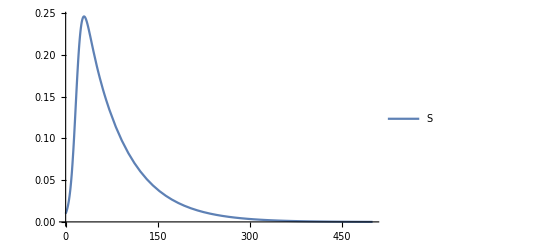

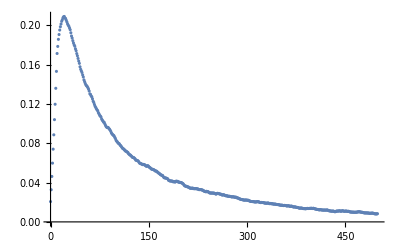

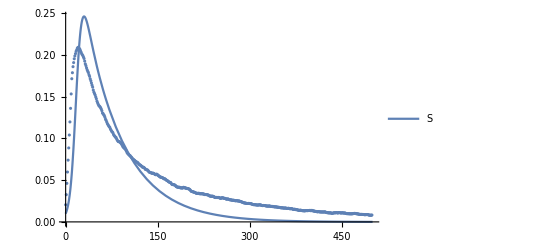

```mathematica
bt=0.7;b=0; c=.45; m=.03;a=1-b-c; T=10;
system={
s'[t]==-bt s[t] i[t]+m(1-b-c)i[t-T],
i'[t]==bt s[t] i[t]-m(a+b+c) i[t-T], 
r'[t]==m b i[t-T],
p'[t]==m c i[t-T],
s[0]==.3-.01,i[0]==.01, r[0]==0, p[0]==0};
sol=NDSolve[system,{s,i,r,p},{t,0,500}]
bplot=Plot[Evaluate[{i[t]}/.sol],{t,0,500},PlotRange->Full,PlotLegends->{"S","I","R","P"}]
tplot=ListPlot[data2]
Show[bplot,tplot]
```

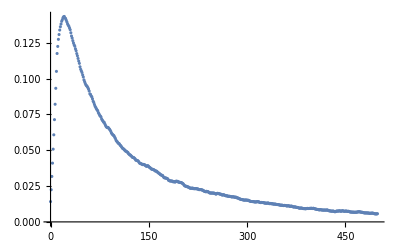

```mathematica
tplot=ListPlot[data]
```

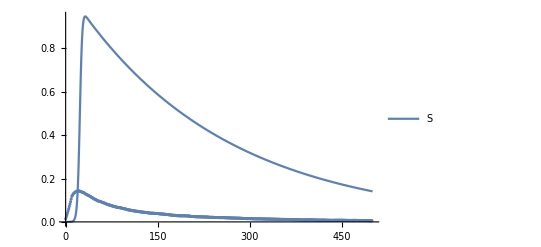

```mathematica
Show[bplot,tplot]
```

Just made a change